## 3D infinite potential well

### Constants

```mathematica
ℏ=1;
M=1;
```

### Dimensions

```mathematica
a=1;
b=√(π/3);
c=√(E/3);
b//N
c//N
```

1.02333

0.95189

### Spectrum

```mathematica
spectrum[nx_,ny_,nz_]:=(ℏ^2 π^2)/(2M) (nx^2/a^2+ny^2/b^2+nz^2/c^2)
```

Required number of states:

```mathematica
Ntotal=100000;
```

Estimated maximum energy (using the semiclassical level density) :

```mathematica
Emax=1.1*(Ntotal (3 π^2 ℏ^3)/(a b c M √(2M)))^(2/3)
```

13688.5

Estimated maximum indices nx, ny :

```mathematica
p=√(Emax (2M)/(π ℏ)^2);
nxmax=Round[p a+1]
nymax=Round[p b+1]
nzmax=Round[p c+1]
```

52

75

59

Sorted levels:

```mathematica
energies=Sort[Select[Flatten[Table[spectrum[nx,ny,nz],{nx,1,nxmax},{ny,1,nymax},{nz,1,nymax}]],#<Emax&]//N];
energies=energies[[1;;Ntotal]];
```

### Unfolding

Integrated smooth level density:

```mathematica
CumulLD[e_]:=(a b c)/(6 π^2)((2M)/ℏ^2)^(3/2)e^(3/2)
```

How well  the exact formula correspond with the data?

```mathematica
cumulLDdata=Transpose[{energies,Table[j,{j,1,Ntotal}]}];
```

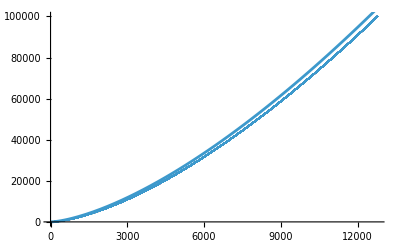

```mathematica
Show[{ListPlot[cumulLDdata],Plot[CumulLD[e],{e,0,Emax}]}]
```

... could be better

#### Unfolding using the semiclassical formula

```mathematica
unfolded=CumulLD[energies];
```

Additional streching - subtracting the first element and dividing by the last one

```mathematica
unfolded=unfolded-unfolded[[1]];
unfolded=unfolded Ntotal/unfolded[[-1]];
```

Unfolded Level density :

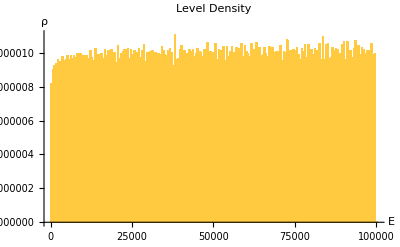

```mathematica
Histogram[unfolded,200,"PDF",PlotLabel->"Level Density",AxesLabel->{"E","ρ"}]
```

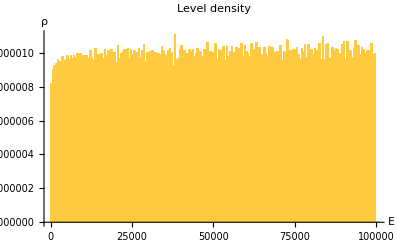

```mathematica
Histogram[unfolded,200,"PDF",PlotLabel->"Level density",AxesLabel->{"E","ρ"}]
```

Level spacing and histogram

```mathematica
spacings=Differences[unfolded];
```

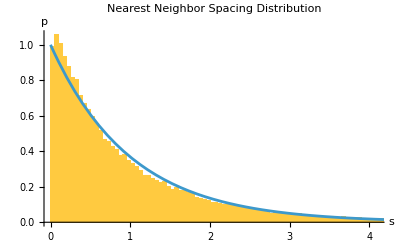

```mathematica
Show[{Histogram[spacings,200,"PDF",PlotLabel->"Nearest Neighbor Spacing Distribution",AxesLabel->{"s","p"}],Plot[Exp[-x],{x,0,5}]}]
```

#### Polynomial unfolding

Degree of the polynomial :

```mathematica
d=6;
```

```mathematica
fit=Fit[cumulLDdata,Table[x^k,{k,0,d}],x]
```

-194.351+1.20072 x+0.00109064 x^2-1.11749×10^-7 x^3+9.92925×10^-12 x^4-4.99562×10^-16 x^5+1.04385×10^-20 x^6

```mathematica
unfolded=fit/.x->energies
```

Unfolded Level density :

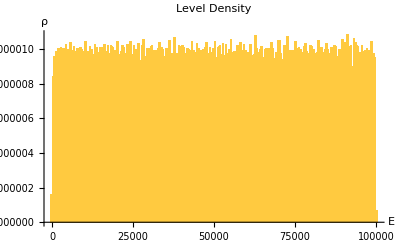

```mathematica
Histogram[unfolded,200,"PDF",PlotLabel->"Level Density",AxesLabel->{"E","ρ"}]
```

Level spacing and histogram

```mathematica
spacings=Differences[unfolded];
```

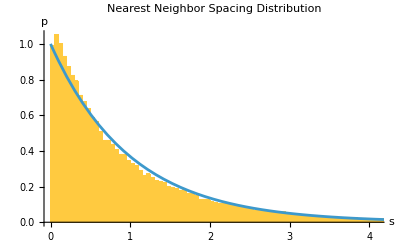

```mathematica
Show[{Histogram[spacings,200,"PDF",PlotLabel->"Nearest Neighbor Spacing Distribution",AxesLabel->{"s","p"}],Plot[Exp[-x],{x,0,5}]}]
```

### Ratios of consecutive spacings

```mathematica
spacings=Differences[energies];
ratios=spacings[[2;;-1]]/spacings[[1;;-2]];
ratiost=If[#>1,1/#,#]&/@ratios;
```

Mean value:

```mathematica
Mean[ratiost]
```

0.381366

Theoretically it should be

```mathematica
2Log[2]-1//N
```

0.386294

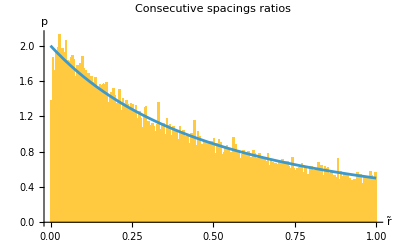

```mathematica
Show[{Histogram[ratiost,200,"PDF",PlotLabel->"Consecutive spacings ratios",AxesLabel->{"r̃","p"}],Plot[2/(1+x)^2,{x,0,1}]}]
```

## 3D anisotropic harmonic oscillator

### Constants

```mathematica
ℏ=1;
M=1;
```

### Frequencies

```mathematica
a=1;
b=√(π/3);
c=√(E/3);
b//N
c//N
```

1.02333

0.95189

... or let us take the frequencies randomly

```mathematica
a=RandomVariate[NormalDistribution[1,0.1]]
b=RandomVariate[NormalDistribution[1,0.1]]
b=RandomVariate[NormalDistribution[1,0.1]]
```

0.887758

1.13403

1.01196

### Spectrum

```mathematica
spectrum[nx_,ny_,nz_]:=ℏ (a nx+b ny+c nz+3/2)
```

Required number of states:

```mathematica
Ntotal=100000;
```

Estimated maximum energy (using the semiclassical level density) :

```mathematica
Emax=1.1*ℏ(6 a b c Ntotal)^(1/3)
```

88.0625

Estimated maximum indices nx, ny, nz:

```mathematica
p=Emax/ℏ;
nxmax=Round[p/a+1]
nymax=Round[p/b+1]
nzmax=Round[p/c+1]
```

100

88

94

Sorted levels:

```mathematica
energies=Sort[Select[Flatten[Table[spectrum[nx,ny,nz],{nx,1,nxmax},{ny,1,nymax},{nz,1,nymax}]],#<Emax&]//N];
energies=energies[[1;;Ntotal]];
```

### Unfolding

Integrated smooth level density:

```mathematica
CumulLD[e_]:=1/6 e^3/(ℏ^3 a b c)
```

How well  the exact formula correspond with the data?

```mathematica
cumulLDdata=Transpose[{energies,Table[j,{j,1,Ntotal}]}];
```

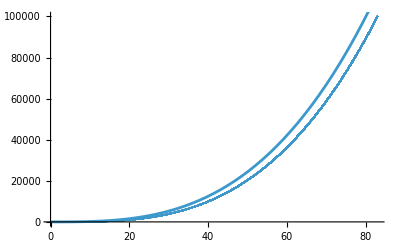

```mathematica
Show[{ListPlot[cumulLDdata],Plot[CumulLD[e],{e,0,Emax}]}]
```

... quite bad, actually

#### Unfolding using the semiclassical formula

```mathematica
unfolded=CumulLD[energies];
```

Additional streching - subtracting the first element and dividing by the last one

```mathematica
unfolded=unfolded-unfolded[[1]];
unfolded=unfolded Ntotal/unfolded[[-1]];
```

Unfolded Level density :

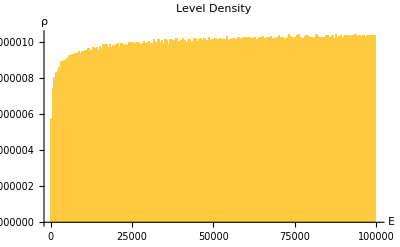

```mathematica
Histogram[unfolded,200,"PDF",PlotLabel->"Level Density",AxesLabel->{"E","ρ"}]
```

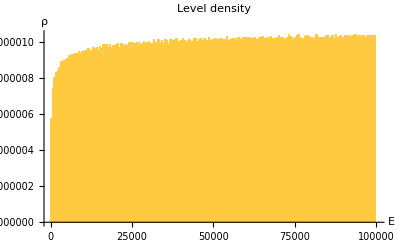

```mathematica
Histogram[unfolded,200,"PDF",PlotLabel->"Level density",AxesLabel->{"E","ρ"}]
```

Level spacing and histogram

```mathematica
spacings=Differences[unfolded];
```

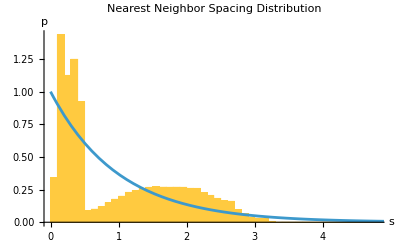

```mathematica
Show[{Histogram[spacings,200,"PDF",PlotLabel->"Nearest Neighbor Spacing Distribution",AxesLabel->{"s","p"}],Plot[Exp[-x],{x,0,5}]}]
```

#### Polynomial unfolding

Degree of the polynomial :

```mathematica
d=6;
```

```mathematica
fit=Fit[cumulLDdata,Table[x^k,{k,0,d}],x]
```

-3.55931+4.79043 x-1.70488 x^2+0.194697 x^3+3.59849×10^-6 x^4-3.24839×10^-8 x^5+1.16064×10^-10 x^6

```mathematica
unfolded=fit/.x->energies
```

Unfolded Level density :

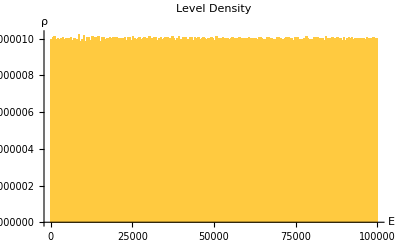

```mathematica
Histogram[unfolded,200,"PDF",PlotLabel->"Level Density",AxesLabel->{"E","ρ"}]
```

Level spacing and histogram

```mathematica
spacings=Differences[unfolded];
```

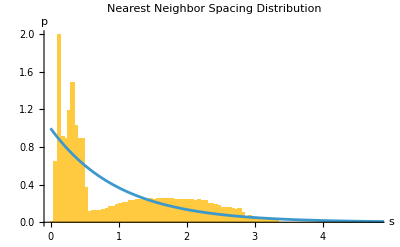

```mathematica
Show[{Histogram[spacings,200,"PDF",PlotLabel->"Nearest Neighbor Spacing Distribution",AxesLabel->{"s","p"}],Plot[Exp[-x],{x,0,5}]}]
```

### Ratios of consecutive spacings

```mathematica
spacings=Differences[energies];
ratios=spacings[[2;;-1]]/spacings[[1;;-2]];
ratiost=If[#>1,1/#,#]&/@ratios;
```

Mean value:

```mathematica
Mean[ratiost]
```

0.353409

Theoretically it should be

```mathematica
2Log[2]-1//N
```

0.386294

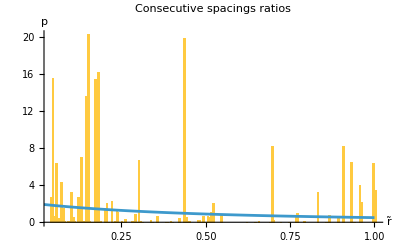

```mathematica
Show[{Histogram[ratiost,200,"PDF",PlotLabel->"Consecutive spacings ratios",AxesLabel->{"r̃","p"}],Plot[2/(1+x)^2,{x,0,1}]}]
```